```mathematica
Clear["Global`*"]
```

```mathematica
M:=0.0004342749552115151
p:=4
μ:=1
ϕini:=0.045514175860860345
ϕend:=0.659399152881071
V[p_,μ_,t_]:=M^4 (1-(ϕ[t]/μ)^p)
Vp[p_,μ_,t_]=D[V[p,μ,t],ϕ[t]];
sol=NDSolve[{3 a'[t]/a[t] ϕ'[t]+Vp[p,μ,t]==0,
a'[t]-a[t]Sqrt[1/3 V[p,μ,t]]==0,ϕ[0]==ϕini,a[0]==1},{ϕ,a},{t,0,1 10^7}];
asr[t_]:=(a/.First[sol])[t]
asrp[t_]=D[asr[t],{t,1}];
ϕsr[t_]:=(ϕ/.First[sol])[t]
ϕsrp[t_]=D[ϕsr[t],{t,1}];
Vt[p_,μ_,t_]:= M^4 (1-(ϕsr[t]/μ)^p)
Hsr[p_,μ_,t_]:=1/Sqrt[3]Sqrt[Vt[p,μ,t]]
Vphi[p_,μ_,ϕ_]:=M^4 (1-(ϕ/μ)^p)
Vp[p_,μ_,ϕ_]=D[V[p,μ,ϕ],{ϕ,1}];
Vpp[f_,ϕ_]=D[V[p,μ,ϕ],{ϕ,2}];
asrp[t_]=D[asr[t],{t,1}];
ϕsrp[t_]=D[ϕsr[t],{t,1}];
ϕsrpp[t_]=D[ϕsr[t],{t,2}];
ϕsrppp[t_]=D[ϕsr[t],{t,3}];
Hsrp[p_,μ_,t_]=D[Hsr[p,μ,t],{t,1}];
(*Parameters*)
ϵH1[p_,μ_,t_]:=-Hsrp[p,μ,t]/Hsr[p,μ,t]^2
ϵH2[p_,μ_,t_]=1/Hsr[p,μ,t] D[ϵH1[p,μ,t],{t,1}];
δH1[p_,μ_,t_]:=ϕsrpp[t]/(Hsr[p,μ,t] ϕsrp[t])
δH2[p_,μ_,t_]:=ϕsrppp[t]/(Hsr[p,μ,t]^2 ϕsrp[t])
α:=0.729637
(*First order*)
PSsr1[t_]:= (1+(4 α-2) ϵH1[p,μ,t]+2 α δH1[p,μ,t]) (Hsr[p,μ,t]^2/(2 π ϕsrp[t]))^2
nSsr1[t_]:=1-4 ϵH1[p,μ,t]-2 δH1[p,μ,t]
PTsr1[t_]:=(1+(2 α-2) ϵH1[p,μ,t])(Hsr[p,μ,t]/(2 π))^2
nTsr1[t_]:=-2 ϵH1[p,μ,t]
(*Second order*)
PSsr2[t_]:=(1+(4 α-2) ϵH1[p,t]+2 α δH1[p,μ,t]+(4 α^2-23+7 π^2/3) ϵH1[p,μ,t]^2+(3 α^2+2α-22+29 π^2/12) ϵH1[p,μ,t] δH1[p,μ,t]+(3 α^2-4+5 π^2/12) δH1[p,μ,t]^2 + (-α^2+π^2/12) δH2[p,μ,t]) (Hsr[p,μ,t]^2/(2 π ϕsrp[t]))^2
nSsr2[t_]:=1-4 ϵH1[p,μ,t]-2 δH1[p,μ,t]+(8 α-8)ϵH1[p,μ,t]^2+(10 α-6) ϵH1[p,μ,t] δH1[p,μ,t]-2 α δH1[p,μ,t]^2+2 α δH2[p,μ,t]
PTsr2[t_]:=(1+(2 α-2) ϵH1[p,μ,t]+(2 α^2-2 α-3+π^2/2) ϵH1[p,μ,t]^2+(-α^2+2 α-2+π^2/12)ϵH2[p,μ,t])(Hsr[p,μ,t]/(2 π))^2
nTsr2[t_]:=-2 ϵH1[p,μ,t]-2 ϵH1[p,μ,t]^2+(2 α-2) ϵH2[p,μ,t]
teval[k_]:=(t/.First[FindRoot[k==asr[t] Hsr[p,μ,t],{t,1000,100000}]])
(*Ration*)
rsr1[t_]:=16 ϵH1[p,μ,t] 
rsr2[t_]:=16 ϵH1[p,μ,t] (1+CC ϵH2[p,μ,t])
CC:=-0.7296 
V[ϕ_]:=M^4 (1-(ϕ/μ)^p)
Vp[ϕ_]=D[V[ϕ],{ϕ,1}];
Vpp[ϕ_]=D[V[ϕ],{ϕ,2}];
ϵ[ϕ_]:=1/2 (Vp[ϕ]/V[ϕ])^2
η[ϕ_]:=Vpp[ϕ]/V[ϕ]
rsrV[ϕ_]:=16 ϵ[ϕ] 
nSsrV[ϕ_]:=-6 ϵ[ϕ]+2 η[ϕ]+1
```

```mathematica
teval[0.05]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

9.12283×10^8

```mathematica
ϕsr[teval[0.002]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
η[ϕsr[teval[0.05]]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

-0.464422

```mathematica
ϵ[ϕend]
```

1.

```mathematica
nSsr1[teval[0.002]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.949889

```mathematica
nSsrV[ϕsr[teval[0.05]]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0683777

```mathematica
rsrV[ϕsr[teval[0.002]]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

0.0000109847

```mathematica
PSsr1[ϕsr[teval[0.05]]]
```

InterpolatingFunction::dmval: Input value {1.21001×10^7} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

2.41768×10^-9

```mathematica
N[ϕini]
```

10.1067

```mathematica
N[ϕend]
```

17.3325

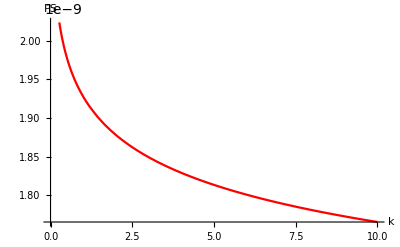

```mathematica
Plot[{PSsr1[teval[k]],PSsr2[teval[k]]},{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,PS}]
```

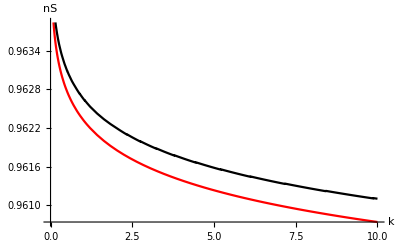

```mathematica
Plot[{nSsr1[teval[k]],nSsr2[teval[k]]},{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,nS}]
```

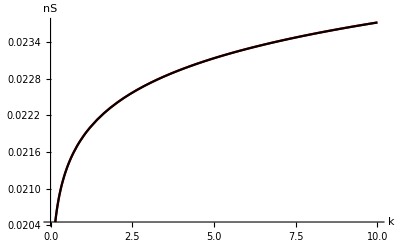

```mathematica
Plot[{rsr1[teval[k]],rsr2[teval[k]]},{k,0.0001,10},PlotStyle->{Red,Black},AxesLabel->{k,nS}]
```